# Three Experiences Binarization And validation using the ODE simulation of Biane Model.

```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
<<Booned`
```

```mathematica
<<Bi4Back`
```

```mathematica
<<Functionsneededpackage`
```

```mathematica
Unprotect[t];Clear[t];Protect[t];
```

## RESEAU BOOLEEN EXEMPLE

```mathematica
FB= {EGFR->!BRCA1,ERK12-> EGFR,PIK3CA->!PTEN&&EGFR,AKT1->PIK3CA,GSK3B->!AKT1, MDM2->AKT1 && TP53,TP53->!MDM2 && (BRCA1|| !PARP1),PTEN->TP53,PARP1->ERK12,BRCA1->¬CCND1,BCL2->AKT1,BAX->!BCL2&&TP53,CCND1->(!GSK3B&&ERK12)||(!BRCA1&&PARP1)}
```

{EGFR→!BRCA1,ERK12→EGFR,PIK3CA→!PTEN&&EGFR,AKT1→PIK3CA,GSK3B→!AKT1,MDM2→AKT1&&TP53,TP53→!MDM2&&(BRCA1||!PARP1),PTEN→TP53,PARP1→ERK12,BRCA1→!CCND1,BCL2→AKT1,BAX→!BCL2&&TP53,CCND1→(!GSK3B&&ERK12)||(!BRCA1&&PARP1)}

```mathematica
Keys[FB]
```

{EGFR,ERK12,PIK3CA,AKT1,GSK3B,MDM2,TP53,PTEN,PARP1,BRCA1,BCL2,BAX,CCND1}

```mathematica
{EGFR,ERK12,PIK3CA,AKT1,GSK3B,MDM2,TP53,PTEN,PARP1,BRCA1,BCL2,BAX,CCND1}
```

{EGFR,ERK12,PIK3CA,AKT1,GSK3B,MDM2,TP53,PTEN,PARP1,BRCA1,BCL2,BAX,CCND1}

```mathematica
StableFB=Association/@StableStates[FB]
```

{<|AKT1→True,BAX→False,BCL2→True,BRCA1→False,CCND1→True,EGFR→True,ERK12→True,GSK3B→False,MDM2→False,PARP1→True,PIK3CA→True,PTEN→False,TP53→False|>,<|AKT1→False,BAX→True,BCL2→False,BRCA1→True,CCND1→False,EGFR→False,ERK12→False,GSK3B→True,MDM2→False,PARP1→False,PIK3CA→False,PTEN→True,TP53→True|>}

```mathematica
Keys[FB]/.StableFB[[1]]
```

{True,True,True,True,False,False,False,False,True,False,True,False,True}

```mathematica
Keys[FB]/.StableFB[[2]]
```

{False,False,False,False,True,False,True,True,False,True,False,True,False}

##### Interaction Graph

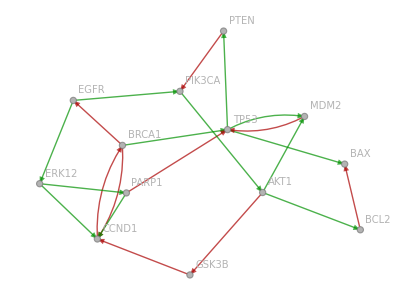

```mathematica
IG=InteractionGraph[FB]
```

## SIMULATION

```mathematica
name="Breast Cancer"
```

Breast Cancer

### Parameters

Expression rate

```mathematica
κ= AssociationThread[Keys[FB],2]
```

<|EGFR→2,ERK12→2,PIK3CA→2,AKT1→2,GSK3B→2,MDM2→2,TP53→2,PTEN→2,PARP1→2,BRCA1→2,BCL2→2,BAX→2,CCND1→2|>

```mathematica
<|EGFR->2,ERK12->2,PIK3CA->2,AKT1->2,GSK3B->2,MDM2->2,Tp53->2,PTEN->2,PARP1->2,BRCA1->2,Bcl2->2,Bax->2,CCND1->2|>
```

<|EGFR→2,ERK12→2,PIK3CA→2,AKT1→2,GSK3B→2,MDM2→2,Tp53→2,PTEN→2,PARP1→2,BRCA1→2,Bcl2→2,Bax→2,CCND1→2|>

Degradation rate

```mathematica
γ=AssociationThread[Keys[FB],0.5]
```

<|EGFR→0.5,ERK12→0.5,PIK3CA→0.5,AKT1→0.5,GSK3B→0.5,MDM2→0.5,TP53→0.5,PTEN→0.5,PARP1→0.5,BRCA1→0.5,BCL2→0.5,BAX→0.5,CCND1→0.5|>

Threshold for being activated or inhibited.

```mathematica
θ=<|EGFR->0.5032031989170531,ERK12->0.5693796586071573,PIK3CA->0.3622517897936625,AKT1->0.6092773024147233,GSK3B->0.4567421270892082,MDM2->0.5946515712847316,TP53->0.4626952828939602,PTEN->0.5446371140553028,PARP1->0.4455321113459842,BRCA1->0.5447147374986528,BCL2->0.5080007779717102,BAX->0.47060064794845163,CCND1->0.4723525185874273|> (*Threshold are generated randomly using the function Thresholding, see the fuction  in the package Functionsneeded*)
```

<|EGFR→0.503203,ERK12→0.56938,PIK3CA→0.362252,AKT1→0.609277,GSK3B→0.456742,MDM2→0.594652,TP53→0.462695,PTEN→0.544637,PARP1→0.445532,BRCA1→0.544715,BCL2→0.508001,BAX→0.470601,CCND1→0.472353|>

```mathematica
Highlighted[TableForm[{Mean[θ],StandardDeviation[θ]}]]
```

0.503388
0.0685953

### For a stable state

```mathematica
stablestate=StableFB[[1]]
```

<|AKT1→True,BAX→False,BCL2→True,BRCA1→False,CCND1→True,EGFR→True,ERK12→True,GSK3B→False,MDM2→False,PARP1→True,PIK3CA→True,PTEN→False,TP53→False|>

```mathematica
<|AKT1->True,Bax->False,Bcl2->True,BRCA1->False,CCND1->True,EGFR->True,ERK12->True,GSK3B->False,MDM2->False,PARP1->True,PIK3CA->True,PTEN->False,Tp53->False|>
```

<|AKT1→True,Bax→False,Bcl2→True,BRCA1→False,CCND1→True,EGFR→True,ERK12→True,GSK3B→False,MDM2→False,PARP1→True,PIK3CA→True,PTEN→False,Tp53→False|>

```mathematica
initialcondition=AssociationThread[Keys[FB], Join[ConstantArray[3,5],ConstantArray[2,5],ConstantArray[1.5,3]]]
```

<|EGFR→3,ERK12→3,PIK3CA→3,AKT1→3,GSK3B→3,MDM2→2,TP53→2,PTEN→2,PARP1→2,BRCA1→2,BCL2→1.5,BAX→1.5,CCND1→1.5|>

```mathematica
<|EGFR->3,ERK12->3,PIK3CA->3,AKT1->3,GSK3B->3,MDM2->2,Tp53->2,PTEN->2,PARP1->2,BRCA1->2,Bcl2->1.5,Bax->1.5,CCND1->1.5|>
```

<|EGFR→3,ERK12→3,PIK3CA→3,AKT1→3,GSK3B→3,MDM2→2,Tp53→2,PTEN→2,PARP1→2,BRCA1→2,Bcl2→1.5,Bax→1.5,CCND1→1.5|>

#### ODE

```mathematica
system={{EGFR'[t]==-0.5 EGFR[t]+2 hillm[BRCA1[t],0.5447147374986528]}, {EGFR[0]==3}, {ERK12'[t]==-0.5 ERK12[t]+2 hillp[EGFR[t],0.5032031989170531]}, {ERK12[0]==3}, {PIK3CA'[t]==2 hillm[PTEN[t],0.5446371140553028] hillp[EGFR[t],0.5032031989170531]-0.5 PIK3CA[t]}, {PIK3CA[0]==3}, {AKT1'[t]==-0.5 AKT1[t]+2 hillp[PIK3CA[t],0.3622517897936625]}, {AKT1[0]==3}, {GSK3B'[t]==-0.5 GSK3B[t]+2 hillm[AKT1[t],0.6092773024147233]}, {GSK3B[0]==3}, {MDM2'[t]==2 hillp[AKT1[t],0.6092773024147233] hillp[TP53[t],0.4626952828939602]-0.5 MDM2[t]}, {MDM2[0]==2}, {TP53'[t]==2 hillm[MDM2[t],0.5946515712847316] (hillm[PARP1[t],0.4455321113459842]+hillp[BRCA1[t],0.5447147374986528])-0.5 TP53[t]}, {TP53[0]==2}, {PTEN'[t]==2 hillp[TP53[t],0.4626952828939602]-0.5 PTEN[t]}, {PTEN[0]==2}, {PARP1'[t]==2 hillp[ERK12[t],0.5693796586071573]-0.5 PARP1[t]}, {PARP1[0]==2}, {BRCA1'[t]==-0.5 BRCA1[t]+2 hillm[CCND1[t],0.4723525185874273]}, {BRCA1[0]==2}, {BCL2'[t]==-0.5 BCL2[t]+2 hillp[AKT1[t],0.6092773024147233]}, {BCL2[0]==1.5}, {BAX'[t]==-0.5 BAX[t]+2 hillm[BCL2[t],0.5080007779717102] hillp[TP53[t],0.4626952828939602]}, {BAX[0]==1.5}, {CCND1'[t]==-0.5 CCND1[t]+2 (hillm[GSK3B[t],0.4567421270892082] hillp[ERK12[t],0.5693796586071573]+hillm[BRCA1[t],0.5447147374986528] hillp[PARP1[t],0.4455321113459842])}, {CCND1[0]==1.5}}
```

{{EGFR'[t]==-0.5 EGFR[t]+2 hillm[BRCA1[t],0.544715]},{EGFR[0]==3},{ERK12'[t]==-0.5 ERK12[t]+2 hillp[EGFR[t],0.503203]},{ERK12[0]==3},{PIK3CA'[t]==2 hillm[PTEN[t],0.544637] hillp[EGFR[t],0.503203]-0.5 PIK3CA[t]},{PIK3CA[0]==3},{AKT1'[t]==-0.5 AKT1[t]+2 hillp[PIK3CA[t],0.362252]},{AKT1[0]==3},{GSK3B'[t]==-0.5 GSK3B[t]+2 hillm[AKT1[t],0.609277]},{GSK3B[0]==3},{MDM2'[t]==2 hillp[AKT1[t],0.609277] hillp[TP53[t],0.462695]-0.5 MDM2[t]},{MDM2[0]==2},{TP53'[t]==2 hillm[MDM2[t],0.594652] (hillm[PARP1[t],0.445532]+hillp[BRCA1[t],0.544715])-0.5 TP53[t]},{TP53[0]==2},{PTEN'[t]==2 hillp[TP53[t],0.462695]-0.5 PTEN[t]},{PTEN[0]==2},{PARP1'[t]==2 hillp[ERK12[t],0.56938]-0.5 PARP1[t]},{PARP1[0]==2},{BRCA1'[t]==-0.5 BRCA1[t]+2 hillm[CCND1[t],0.472353]},{BRCA1[0]==2},{BCL2'[t]==-0.5 BCL2[t]+2 hillp[AKT1[t],0.609277]},{BCL2[0]==1.5},{BAX'[t]==-0.5 BAX[t]+2 hillm[BCL2[t],0.508001] hillp[TP53[t],0.462695]},{BAX[0]==1.5},{CCND1'[t]==-0.5 CCND1[t]+2 (hillm[GSK3B[t],0.456742] hillp[ERK12[t],0.56938]+hillm[BRCA1[t],0.544715] hillp[PARP1[t],0.445532])},{CCND1[0]==1.5}}

#### Experiments

```mathematica
exp=ThreeExperienceFromODE[FB,system,25,stablestate,θ]
```

<|9.77→<|EGFR→3.06,ERK12→3.09,PIK3CA→2.22,AKT1→2.28,GSK3B→0.452,MDM2→0.246,TP53→0.115,PTEN→0.246,PARP1→3.98,BRCA1→0.131,BCL2→3.55,BAX→0.0113,CCND1→4.69|>,17.37→<|EGFR→3.98,ERK12→3.98,PIK3CA→3.96,AKT1→3.96,GSK3B→0.0101,MDM2→0.00549,TP53→0.00257,PTEN→0.00549,PARP1→4.,BRCA1→0.00294,BCL2→3.99,BAX→0.000254,CCND1→7.93|>,25.→<|EGFR→4.,ERK12→4.,PIK3CA→4.,AKT1→4.,GSK3B→0.000223,MDM2→0.000121,TP53→0,PTEN→0.000121,PARP1→4.,BRCA1→0,BCL2→4.,BAX→0,CCND1→8.|>|>

```mathematica
Epil=Keys[exp];
```

```mathematica
fun=#[t]&/@Keys[FB];
```

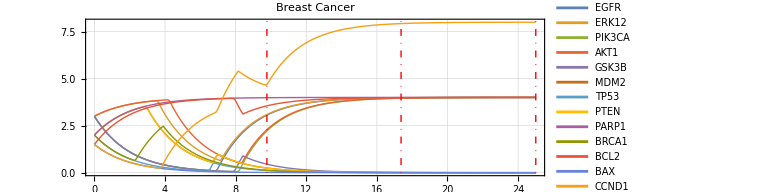

```mathematica
FigBreast1=Plot[Evaluate[fun/.NDSolve[system,Keys[FB],{t,0,25}]],{t,0,25}, PlotRange->All, PlotTheme->"Detailed",PlotStyle->Thick,PlotLegends->Placed[Keys[FB],Right],LabelStyle->Directive[FontFamily->"Franklin Gothic",11],
AspectRatio->1/3, PlotLabel-> name, ImageSize->Large,Epilog-> {Thick,DotDashed, Red, Line[{{Epil[[1]],0},{Epil[[1]],10}}] ,Line[{{Epil[[2]],0},{Epil[[2]],10}}], Line[{{Epil[[3]],0},{Epil[[3]],10}}]}]
```

```mathematica
result=ThreeExperimentsBinarisation[IG,Values[exp] , stablestate];
```

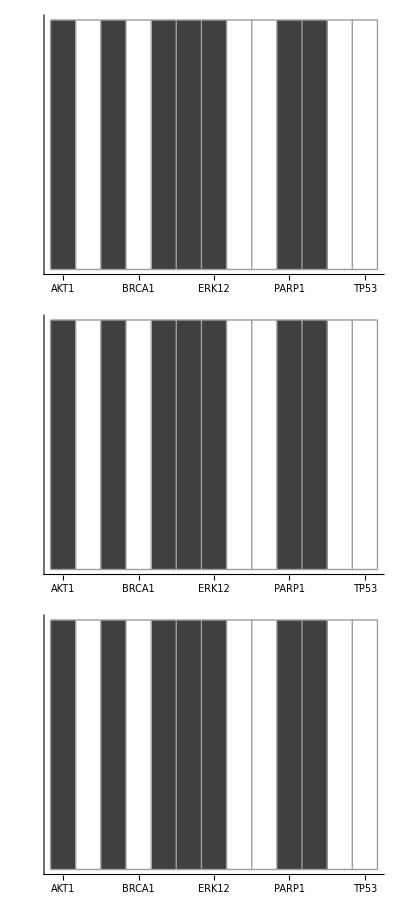

```mathematica
TableForm[Function[profile, ArrayPlot[{Values[profile]}, ColorRules->{True -> GrayLevel[0.25],False->White},Mesh->All, ImageSize->Large,
Axes->{True,False}, Ticks->{Thread[{Range[0.5,Length[profile]-0.5,1],Keys[profile]}],None}]]/@result]
```

```mathematica
dis=Distanceofdissimilarity[result,stablestate] (*voir la fonction dans le package functionsneeded*)
```

{0,0,0}

### For stable state

```mathematica
stablestate=StableFB[[2]]
```

<|AKT1→False,BAX→True,BCL2→False,BRCA1→True,CCND1→False,EGFR→False,ERK12→False,GSK3B→True,MDM2→False,PARP1→False,PIK3CA→False,PTEN→True,TP53→True|>

```mathematica
<|AKT1->False,Bax->True,Bcl2->False,BRCA1->True,CCND1->False,EGFR->False,ERK12->False,GSK3B->True,MDM2->False,PARP1->False,PIK3CA->False,PTEN->True,Tp53->True|>
```

<|AKT1→False,Bax→True,Bcl2→False,BRCA1→True,CCND1→False,EGFR→False,ERK12→False,GSK3B→True,MDM2→False,PARP1→False,PIK3CA→False,PTEN→True,Tp53→True|>

```mathematica
initialcondition=<|EGFR->0.3,ERK12->0.4,PIK3CA->0.4,AKT1->0.4,GSK3B->1,MDM2->0.3,TP53->1,PTEN->1,PARP1->0.4,BRCA1->1,BCL2->0.4,BAX->1,CCND1->0.3|>
```

<|EGFR→0.3,ERK12→0.4,PIK3CA→0.4,AKT1→0.4,GSK3B→1,MDM2→0.3,TP53→1,PTEN→1,PARP1→0.4,BRCA1→1,BCL2→0.4,BAX→1,CCND1→0.3|>

#### ODE

```mathematica
system={{EGFR'[t]==-0.5 EGFR[t]+2 hillm[BRCA1[t],0.5447147374986528]}, {EGFR[0]==0.3}, {ERK12'[t]==-0.5 ERK12[t]+2 hillp[EGFR[t],0.5032031989170531]}, {ERK12[0]==0.4}, {PIK3CA'[t]==2 hillm[PTEN[t],0.5446371140553028] hillp[EGFR[t],0.5032031989170531]-0.5 PIK3CA[t]}, {PIK3CA[0]==0.4}, {AKT1'[t]==-0.5 AKT1[t]+2 hillp[PIK3CA[t],0.3622517897936625]}, {AKT1[0]==0.4}, {GSK3B'[t]==-0.5 GSK3B[t]+2 hillm[AKT1[t],0.6092773024147233]}, {GSK3B[0]==1}, {MDM2'[t]==2 hillp[AKT1[t],0.6092773024147233] hillp[TP53[t],0.4626952828939602]-0.5 MDM2[t]}, {MDM2[0]==0.3}, {TP53'[t]==2 hillm[MDM2[t],0.5946515712847316] (hillm[PARP1[t],0.4455321113459842]+hillp[BRCA1[t],0.5447147374986528])-0.5 TP53[t]}, {TP53[0]==1}, {PTEN'[t]==2 hillp[TP53[t],0.4626952828939602]-0.5 PTEN[t]}, {PTEN[0]==1}, {PARP1'[t]==2 hillp[ERK12[t],0.5693796586071573]-0.5 PARP1[t]}, {PARP1[0]==0.4}, {BRCA1'[t]==-0.5 BRCA1[t]+2 hillm[CCND1[t],0.4723525185874273]}, {BRCA1[0]==1}, {BCL2'[t]==-0.5 BCL2[t]+2 hillp[AKT1[t],0.6092773024147233]}, {BCL2[0]==0.4}, {BAX'[t]==-0.5 BAX[t]+2 hillm[BCL2[t],0.5080007779717102] hillp[TP53[t],0.4626952828939602]}, {BAX[0]==1}, {CCND1'[t]==-0.5 CCND1[t]+2 (hillm[GSK3B[t],0.4567421270892082] hillp[ERK12[t],0.5693796586071573]+hillm[BRCA1[t],0.5447147374986528] hillp[PARP1[t],0.4455321113459842])}, {CCND1[0]==0.3}}
```

{{EGFR'[t]==-0.5 EGFR[t]+2 hillm[BRCA1[t],0.544715]},{EGFR[0]==0.3},{ERK12'[t]==-0.5 ERK12[t]+2 hillp[EGFR[t],0.503203]},{ERK12[0]==0.4},{PIK3CA'[t]==2 hillm[PTEN[t],0.544637] hillp[EGFR[t],0.503203]-0.5 PIK3CA[t]},{PIK3CA[0]==0.4},{AKT1'[t]==-0.5 AKT1[t]+2 hillp[PIK3CA[t],0.362252]},{AKT1[0]==0.4},{GSK3B'[t]==-0.5 GSK3B[t]+2 hillm[AKT1[t],0.609277]},{GSK3B[0]==1},{MDM2'[t]==2 hillp[AKT1[t],0.609277] hillp[TP53[t],0.462695]-0.5 MDM2[t]},{MDM2[0]==0.3},{TP53'[t]==2 hillm[MDM2[t],0.594652] (hillm[PARP1[t],0.445532]+hillp[BRCA1[t],0.544715])-0.5 TP53[t]},{TP53[0]==1},{PTEN'[t]==2 hillp[TP53[t],0.462695]-0.5 PTEN[t]},{PTEN[0]==1},{PARP1'[t]==2 hillp[ERK12[t],0.56938]-0.5 PARP1[t]},{PARP1[0]==0.4},{BRCA1'[t]==-0.5 BRCA1[t]+2 hillm[CCND1[t],0.472353]},{BRCA1[0]==1},{BCL2'[t]==-0.5 BCL2[t]+2 hillp[AKT1[t],0.609277]},{BCL2[0]==0.4},{BAX'[t]==-0.5 BAX[t]+2 hillm[BCL2[t],0.508001] hillp[TP53[t],0.462695]},{BAX[0]==1},{CCND1'[t]==-0.5 CCND1[t]+2 (hillm[GSK3B[t],0.456742] hillp[ERK12[t],0.56938]+hillm[BRCA1[t],0.544715] hillp[PARP1[t],0.445532])},{CCND1[0]==0.3}}

## Experiments

```mathematica
exp=ThreeExperienceFromODE[FB,system,25,stablestate,θ] (*voir la fonction dans le package functionsneeded*)
```

<|2.22→<|EGFR→0.0989,ERK12→0.132,PIK3CA→0.132,AKT1→0.27,GSK3B→2.64,MDM2→0.469,TP53→2.44,PTEN→3.01,PARP1→0.132,BRCA1→3.01,BCL2→0.502,BAX→0.54,CCND1→0.0989|>,13.59→<|EGFR→0.000336,ERK12→0.000448,PIK3CA→0.000448,AKT1→0.000917,GSK3B→4.,MDM2→0.00159,TP53→7.98,PTEN→4.,PARP1→0.000448,BRCA1→4.,BCL2→0.0017,BAX→3.99,CCND1→0.000336|>,25.→<|EGFR→0,ERK12→0,PIK3CA→0,AKT1→0,GSK3B→4.,MDM2→0,TP53→8.,PTEN→4.,PARP1→0,BRCA1→4.,BCL2→0,BAX→4.,CCND1→0|>|>

```mathematica
Epil=Keys[exp]
```

{2.22,13.59,25.}

```mathematica
fun=#[t]&/@Keys[FB];
```

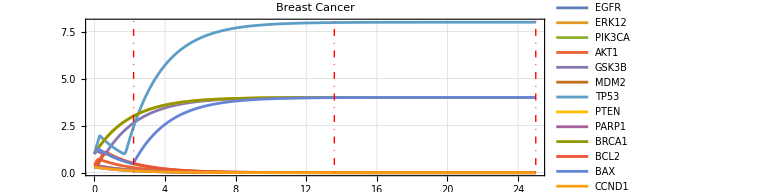

```mathematica
Plot[Evaluate[fun/.NDSolve[system,Keys[FB],{t,0,25}]],{t,0,25}, PlotRange->All, PlotTheme->"Detailed",PlotStyle->Thick,PlotLegends->Placed[Keys[FB],Right],LabelStyle->Directive[FontFamily->"Franklin Gothic",11],
AspectRatio->1/3, PlotLabel-> name, ImageSize->Large,Epilog-> {Thick,DotDashed, Red, Line[{{Epil[[1]],0},{Epil[[1]],10}}] ,Line[{{Epil[[2]],0},{Epil[[2]],10}}], Line[{{Epil[[3]],0},{Epil[[3]],10}}]}]
```

```mathematica
result=ThreeExperimentsBinarisation[IG,Values[exp], stablestate](*voir la fonction dans le package functionsneeded*)
```

{<|AKT1→False,BAX→True,BCL2→False,BRCA1→True,CCND1→False,EGFR→False,ERK12→False,GSK3B→True,MDM2→False,PARP1→False,PIK3CA→False,PTEN→True,TP53→True|>,<|AKT1→False,BAX→True,BCL2→False,BRCA1→True,CCND1→False,EGFR→False,ERK12→False,GSK3B→True,MDM2→False,PARP1→False,PIK3CA→False,PTEN→True,TP53→True|>,<|AKT1→False,BAX→True,BCL2→False,BRCA1→True,CCND1→False,EGFR→False,ERK12→False,GSK3B→True,MDM2→False,PARP1→False,PIK3CA→False,PTEN→True,TP53→True|>}

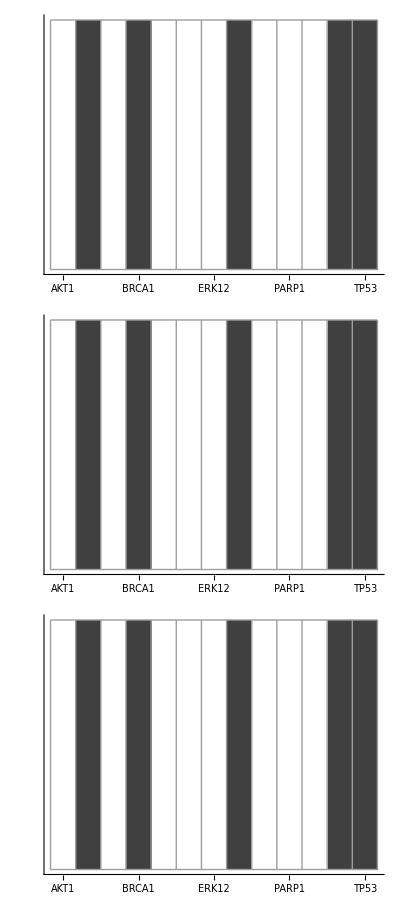

```mathematica
TableForm[Function[profile, ArrayPlot[{Values[profile]}, ColorRules->{True -> GrayLevel[0.25],False->White},Mesh->All, ImageSize->Large,
Axes->{True,False}, Ticks->{Thread[{Range[0.5,Length[profile]-0.5,1],Keys[profile]}],None}]]/@result]
```

```mathematica
dis=Distanceofdissimilarity[result,stablestate]
```

{0,0,0}